```mathematica
eC=1.6*10^-19;
Ne=2*10^10;
e0=8.854*10^-12;
```

```mathematica
eR[r_,sigR_,sigZ_]=eC*Ne*(1-Exp[-r^2/(2*sigR^2)])/((2*π)^1.5*e0*sigZ*r);
eRZ[r_,z_,sigR_,sigZ_]=eC*Ne*(1-Exp[-r^2/(2*sigR^2)])*Exp[-z^2/(2*sigZ^2)]/((2*π)^1.5*e0*sigZ*r);
```

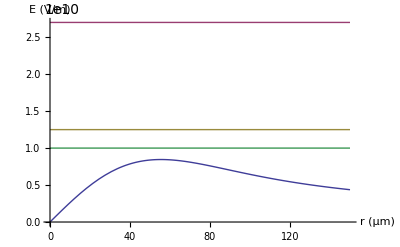

```mathematica
Plot[{eR[x*10^-6,35*10^-6,35*10^-6],2.7*10^10,1.25*10^10,1*10^10},{x,0,150},AxesLabel->{"r (μm)","E (V/m)"}]
```

```mathematica
Plot3D[eRZ[x,y,10*10^-6,20*10^-6],{x,0,100*10^-6},{y,-20*10^-6,20*10^-6}]
```

-Graphics3D-